## INTRO

💡 This is a program for χ^2 fitting, using SN1a data.
💡 SN data are taken from http://supernova.lbl.gov/Union/
💡 
💡
💡

## PRE

### Settings

Include the packages needed.

```mathematica
Needs["ErrorBarPlots`"]
<<PhysicalConstants`
```

```mathematica
Needs["PlotLegends`"]
```

Set work directory. Modify it to your own directory before runing this program. DATA folder are placed in this directory. DATA folder should contain the SN data files.

```mathematica
SetDirectory["E:\\Nutshare\\Store\\Projects\\DataFitting"];
```

### Conventions, parameters, etc

Line element: ds^2=-dt^2+a[t]^2(dr^2/(1-k r^2)+r^2(dθ^2+Sin[θ]^2 dϕ^2))

Ωm0: matter fraction
Ωd0: dark energy/cosmological constant fraction
Ωr0: radiation fraction

Ωm0w: matter fraction given by WMAP
Ωd0w: dark energy/cosmological constant fraction given by WMAP
Ωr0w: radiation fraction given WMAP

```mathematica
Ωm0w=0.27;
Ωd0w=0.73;
Ωr0w =8.09*10^-5;
```

### Basic Equations in LCDM

H0: Hubble constant in unit of km/s/Mpc
c: speed of light

```mathematica
H0w=71;
c=SpeedOfLight*Second/(1000Meter)
gra=GravitationalConstant
```

149896229/500

(6.67428×10^-11 Meter^2 Newton)/Kilogram^2

## LCDM Model

### Basic Definations

hubble[Ωm0_,Ωd0_,Ωk0_,z_]: Hubble functions in LCDM.
H[z]: an example of hubble function with given parameters.

```mathematica
hubble[Ωm0_,Ωd0_,Ωk0_,z_]:=H0w √(Ωm0(1+z)^3+Ωd0+Ωk0(1+z)^2);
H[z_]=hubble[Ωm0w,Ωd0w,0,z];
```

q[Ωm0_,Ωd0_,Ωk0_,z_]:Deceleration parameter. DEF: q[Ωm0_,Ωd0_,Ωk0_,z_]=-1/H[z]D[D[a[t],t],t]/D[a[t],t]

```mathematica
q[Ωm0_,Ωd0_,Ωk0_,z_]=-1+(1+z)/hubble[Ωm0,Ωd0,Ωk0,z] D[hubble[Ωm0,Ωd0,Ωk0,z],z];
```

```mathematica
q[Ωm0,Ωd0,Ωk0,0]
```

-1+(2 Ωk0+3 Ωm0)/(2 (Ωd0+Ωk0+Ωm0))

```mathematica
-1+(2 Ωk0+3 Ωm0)/(2 (Ωd0+Ωk0+Ωm0))
```

-1+(2 Ωk0+3 Ωm0)/(2 (Ωd0+Ωk0+Ωm0))

```mathematica
Limit[q[Ωm0,Ωd0,Ωk0,z],z->Infinity]
```

1/2

(General) Friedmann equations are

(3(a[t]'+k))/a[t]^2=8 π G ρ
2(a[t]'')/a[t]+(a[t]'+k)/a[t]^2=-8π G p

Since “zt” will be used as a parameter in most cases, we define “ztr” as a name for transition redshift, “ztrr” for transition redshift with a parameter r.
ztr[Ωm0_,Ωd0_,z_]: Transition redshift in LCDM with Ωk0 not zero with full parameters
ztrr[r_,z_]: with r=Ωm0/Ωd0

```mathematica
ztr[Ωm0_,Ωd0_]=(2 Ωd0/Ωm0)^(1/3)-1;
ztrr[r_]=(2/r)^(1/3)-1;
```

Regard “zt” as a paramter, solve out Ωd0 and Ωk0=1-Ωm0-Ωd0

Ωd0=1/2 Ωm0(1+zt)^3
Ωk0=1-Ωm0-1/2 Ωm0(1+zt)^3

### Transition redshift, deceleration parameter, theoretically.

#### Deceleration parameter

Deceleration parameter can be ploted with respect to redshift z.
Using flat FRW model. That is Ωk0=0.

```mathematica
pldec[Ωm0v_,color_]:=Plot[q[Ωm0v,1-Ωm0v,0,z],{z,-1,10},PlotRange->{{-1.05,10},{-1.05,0.55}},PlotStyle->color,AxesOrigin->{-1,0},AxesLabel->{z,q}]
```

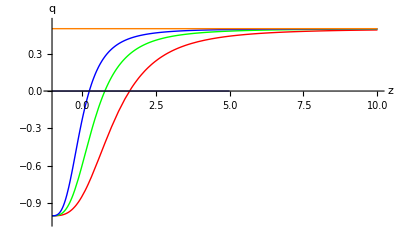

```mathematica
Show[{pldec[0.1,Red],pldec[0.26,Green],pldec[0.5,Blue],pldec[1,Orange],Plot[0,{z,-1,5},PlotStyle->Thick]}]
```

```mathematica
Manipulate[pldec[Ωm0v,{Orange,Thick}],{{Ωm0v,0.26,"Matter Fraction"},0,1,Appearance->"Open"},SaveDefinitions->True]
```

Plot deceleration parameter with respect to r. This is not related to Ωk0, i.e., the curvature of the spacetime won’t affect this result.

```mathematica
plztr[color_]:=Plot[ztr[Ωm0,1-Ωm0],{Ωm0,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->color,AxesOrigin->{0,-1}]
```

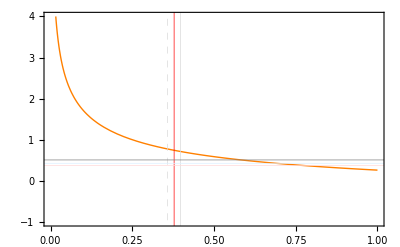

```mathematica
pldecrr=Plot[ztrr[r],{r,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.358,Dashed},{0.378,Directive[Red]},0.398},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}}]
```

In a flat universe, Ωk0=0. Then Ωd0=1-Ωm0.

```mathematica
pldecr=Show[Plot[ztr[Ωm0,1-Ωm0],{Ωm0,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.044,Dashed},{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}}],Graphics[{Gray,Rectangle[Scaled[{0.261,.2752}],Scaled[{0.287,.3016}]]},Frame->True]]
```

-Graphics-

## Interacting Models

### Take the form Q_c=ξ H ρ_d. I2 model

Hubble function without curvature

```mathematica
hubbleI2CC[H0_,Ωd0_,Ωm0_,w_,ξ_,z_]:=H0 √(Ωm+Ωd);
```

Conventions:
parameters : H0, Ωm0, Ωd0, w, ξ, z.

### Constant ξ + CPL w. I2CPL model.

#### Definations

CPL EoS w=w0+w1 z/(1+z)

In the following calculation, some complex numbers will occur. But

Prepare

```mathematica
hubblecmpintI2CCPL[w0_,w1_,ξI2CCPL_,z_?NumberQ]:=Integrate[Exp[3 w1/(1+tmp)-3w1](1+tmp)^(3(w0+w1)+ξI2CCPL-1),{tmp,0,z},Assumptions->{tmp∈Reals&&z∈Reals&&z>-1}]
```

```mathematica
hubblecmpintI2CCPLtest[w0_,w1_,ξI2CCPL_,z_?NumberQ]:=NIntegrate[Exp[3 w1/(1+tmp)-3w1](1+tmp)^(3(w0+w1)+ξI2CCPL-1),{tmp,0,z}]
```

```mathematica
hubblecmpintI2CCPL[-1,0.1,0.1,10]//Timing
Re[%]
hubblecmpintI2CCPLtest[-1,0.1,0.1,10]//Timing
```

{1.154,0.353978-2.63192×10^-15 ⅈ}

{1.154,0.353978}

{0.063,0.353978}

Matter density

```mathematica
ΩmI2CCPL[Ωd0I2CCPL_,Ωm0I2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_]=Ωm0I2CCPL (1+z)^3-ξI2CCPL Ωm0I2CCPL (1+z)^3 hubblecmpintI2CCPL[w0I2CCPL,w1I2CCPL,ξI2CCPL,z];
```

```mathematica
ΩmI2CCPLtest[Ωd0I2CCPL_,Ωm0I2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_?NumberQ]=Ωm0I2CCPL (1+z)^3-ξI2CCPL Ωm0I2CCPL (1+z)^3 hubblecmpintI2CCPLtest[w0I2CCPL,w1I2CCPL,ξI2CCPL,z];
```

```mathematica
ΩdI2CCPL[Ωd0I2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_]:=Ωd0I2CCPL Exp[-3z w1I2CCPL/(1+z)](1+z)^(3(1+w0I2CCPL+w1I2CCPL)+ξI2CCPL)
```

Hubble function.

```mathematica
hubbleI2CCPL[H0I2CCPL_,Ωd0I2CCPL_,Ωm0I2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_]=H0I2CCPL√(ΩmI2CCPL[Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]+ΩdI2CCPL[Ωd0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]);
```

```mathematica
hubbleI2CCPLtest[H0I2CCPL_,Ωd0I2CCPL_,Ωm0I2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_?NumberQ]=H0I2CCPL√(ΩmI2CCPLtest[Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]+ΩdI2CCPL[Ωd0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]);
```

```mathematica
hubbleDI2CCPL[H0I2CCPL_,Ωd0I2CCPL_,Ωm0I2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_]=D[hubbleI2CCPL[H0I2CCPL,Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z],z];
```

```mathematica
hubbleDI2CCPLtest[H0I2CCPL_,Ωd0I2CCPL_,Ωm0I2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_]=(hubbleI2CCPLtest[H0I2CCPL,Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z+0.001]-hubbleI2CCPLtest[H0I2CCPL,Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z-0.001])/0.002;
```

```mathematica
hubbleI2CCPL[H0w,0.7,0.3,-1,0.1,0.1,10]//Timing
Re[%]
hubbleI2CCPLtest[H0w,0.7,0.3,-1,0.1,0.1,10]//Timing
hubbleDI2CCPL[H0w,0.7,0.3,-1,0.1,0.1,10]//Timing
Re[%]
hubbleDI2CCPLtest[H0w,0.7,0.3,-1,0.1,0.1,10]//Timing
```

{0.655,1395.93+1.89755×10^-13 ⅈ}

{0.655,1395.93}

{0.016,1395.93}

{43.165,189.745+2.59585×10^-14 ⅈ}

{43.165,189.745}

{0.016,189.745}

Check whether this hubble function is reasonable.

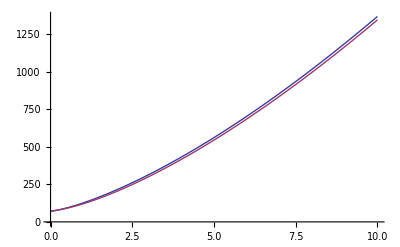

```mathematica
Plot[{hubbleI2CCPLtest[H0w,0.73,0.27,-1,0.6,-0.02,z],hubble[Ωm0w,Ωd0w,0,z]},{z,0,10}]
```

Deceleration parameter

```mathematica
qI2CCPL[H0I2CCPL_,Ωd0I2CCPL_,Ωm0I2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_]=-1+(1+z)/hubbleI2CCPLtest[H0I2CCPL,Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]hubbleDI2CCPLtest[H0I2CCPL,Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z];
```

```mathematica
qI2CCPL[H0w,0.7,0.3,-1,0.1,0.1,10]//Timing
```

{0.032,0.495197}

#### Equation of State

```mathematica
plEoSI2CCPLMan=plEoSICCPLMan
```

plEoSICCPLMan

```mathematica
plEoSPhaseI2CCPL=plEoSPhaseICCPL
```

plEoSPhaseICCPL

#### Plot deceleration parameter and

```mathematica
pldecI2CCPL[Ωm0I2CCPL_,ξI2CCPL_,w0I2CCPL_,w1I2CCPL_,color_]:=Plot[qI2CCPL[H0w,1-Ωm0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z],{z,-1,20},PlotRange->{{-1.05,20},{-1.05,1}},PlotStyle->color,AxesOrigin->{-1,0},AxesLabel->{z,q}];
```

```mathematica
discretepldecI2CCPL[Ωm0I2CCPL_,ξI2CCPL_,w0I2CCPL_,w1I2CCPL_,color_]:=DiscretePlot[qI2CCPL[H0w,1-Ωm0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z],{z,-1,10,1},PlotStyle->color,AxesOrigin->{-1,0},AxesLabel->{z,q}]
```

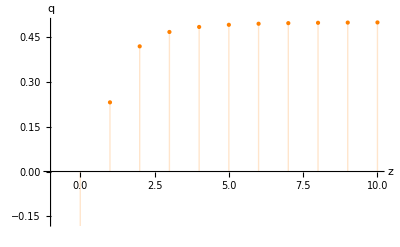
{0.515,-Graphics-}

```mathematica
discretepldecI2CCPL[0.3,-0.4,-1,0.1,Orange]//Timing//Quiet
```

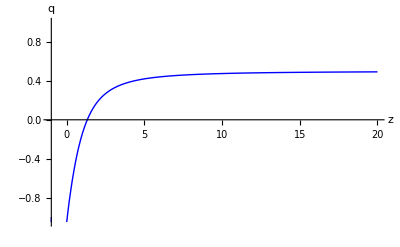
{9.142,-Graphics-}

```mathematica
pldecI2CCPL[0.1,-0.4,-1.02,0.60,Blue]//Timing//Quiet
```

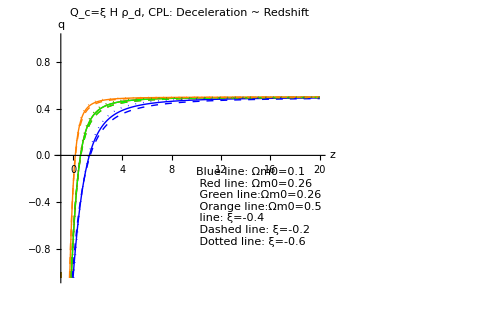

```mathematica
pldecI2CCPLShowSum=Show[{pldecI2CCPL[0.1,-0.4,-1.02,0.60,Blue],pldecI2CCPL[0.26,-0.4,-1.02,0.60,Red],pldecI2CCPL[0.26,-0.4,-1.02,0.60,Green],pldecI2CCPL[0.5,-0.4,-1.02,0.60,Orange],pldecI2CCPL[0.1,-0.2,-1.02,0.60,Directive[Blue,Dashed]],pldecI2CCPL[0.26,-0.2,-1.02,0.60,Directive[Red,Dashed]],pldecI2CCPL[0.26,-0.2,-1.02,0.60,Directive[Green,Dashed]],pldecI2CCPL[0.5,-0.2,-1.02,0.60,Directive[Orange,Dashed]],pldecI2CCPL[0.1,-0.6,-1.02,0.60,Directive[Blue,Dotted]],pldecI2CCPL[0.26,-0.6,-1.02,0.60,Directive[Red,Dotted]],pldecI2CCPL[0.26,-0.6,-1.02,0.60,Directive[Green,Dotted]],pldecI2CCPL[0.5,-0.6,-1.02,0.60,Directive[Orange,Dotted]]},Epilog->Inset[Framed[Style["Blue line: Ωm0=0.1\n Red line: Ωm0=0.26\n Green line:Ωm0=0.26\n Orange line:Ωm0=0.5\n line: ξ=-0.4\n Dashed line: ξ=-0.2\n Dotted line: ξ=-0.6",10],Background->LightGreen,FrameStyle->None],{10,-0.1},{Left,Top}],PlotLabel->"Q_c=ξ H ρ_d, CPL: Deceleration ~ Redshift",ImageSize->500]//Quiet
```

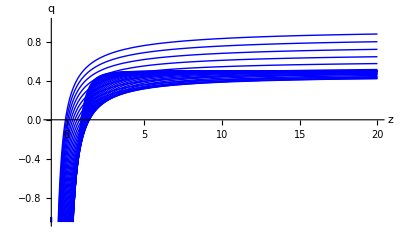
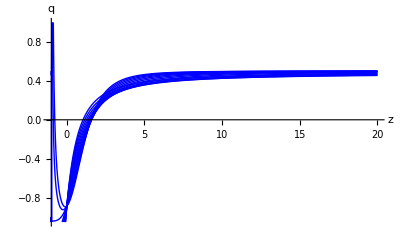
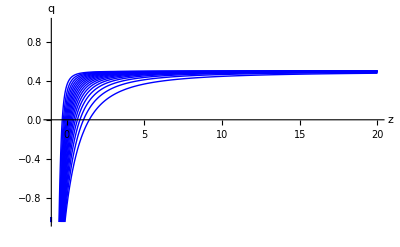
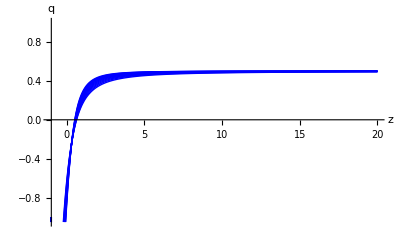
Q_c=ξ H ρ_d, CPL |  |  | 
Varying CPL w0 | Varying CPL w1 | Varying Ωm0 | Varying ξ
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
varyingI2CCPLShowSum=Grid[{{"Q_c=ξ H ρ_d, CPL",SpanFromLeft},{"Varying CPL w0","Varying CPL w1","Varying Ωm0","Varying ξ"},{Show[Table[pldecI2CCPL[0.1,-0.02,w0I2CCPL,0.6,Blue],{w0I2CCPL,-2,-0.3,0.05}]],Show[Table[pldecI2CCPL[0.1,-0.02,-1.02,w1I2CCPL,Blue],{w1I2CCPL,-0.2,1,0.1}]],Show[Table[pldecI2CCPL[Ωm0I2CCPL,-0.02,-1.02,0.6,Blue],{Ωm0I2CCPL,0.1,0.9,0.05}]],Show[Table[pldecI2CCPL[0.27,ξI2CCPL,-1.02,0.6,Blue],{ξI2CCPL,-1,0,0.1}]]}},Frame->All,Background->{{None},{LightGreen,None}}]//Quiet
```

```mathematica
(* Do not run the following if not needed. *)
pldecI2CCPLManSum=Manipulate[Show[{pldecI2CCPL[Ωm0I2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL,Orange],pldec[Ωm0I2CCPL,{Pink,Thick}]},PlotLabel->"Q_c=ξ H ρ_d,CPL: Deceleration ~ Redshift"],{{Ωm0I2CCPL,0.26,"Matter Fraction"},0,1,Appearance->"Open"},{{ξI2CCPL,-0.4,"Interaction"},-1,0,Appearance->"Open"},{{w0I2CCPL,-1.02,"CPL EoS w0"},-2,-0.3,Appearance->"Open"},{{w1I2CCPL,0.6,"CPL EoS w1"},-0.2,1,Appearance->"Open"},Delimiter,Style["Pink is the deceleration parameter for LCDM.",Medium],Style["Orange is for interacting CPL model with Q=ξ H ρ_d",Medium],ControlPlacement->{Right,Right,Right},SaveDefinitions->True]//Quiet
```

#### Transition Redshift

Find out the expression for transition redshift

```mathematica
ztrI2CCPL[Ωm0I2CCPL_,Ωd0I2CCPL_,ξI2CCPL_,w0I2CCPL_,w1I2CCPL_]:=z/.FindRoot[(1+3(w0I2CCPL+w1I2CCPL z/(1+z)))ΩdI2CCPL[Ωd0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]+ΩmI2CCPLtest[Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]==0,{z,3}];
```

```mathematica
ztrI2CCPL[0.3,1-0.3,0,-1,0.1]//Timing
```

{0.218,0.655139}

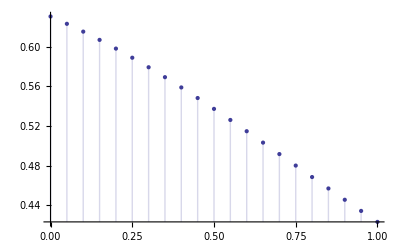

```mathematica
DiscretePlot[{ztrI2CCPL[0.3,1-0.3,-0.1,-1,tmp]},{tmp,0,1,0.05}]//Quiet
```

The following is just used for test.

```mathematica
(*
(*This is a test of how well are the findroot results.*)
Plot[{plottestfunctiontemp[temp,1-temp,-0.1,-0.9,-0.05,ztrICCPLtest2[temp,1-temp,-0.1,-0.9,-0.05]],plottestfunctiontemp[temp,1-temp,-0.1,-0.9,-0.05,ztrICCPLtest[temp,1-temp,-0.1,-0.9,-0.05]],plottestfunctiontemp[temp,1-temp,-0.1,-0.9,-0.05,ztrICCPL[temp,1-temp,-0.1,-0.9,-0.05]]},{temp,0,1},PlotStyle->{Red,Orange,Blue}]
*)
```

Define rICC=Ωm0ICC/Ωd0ICC

```mathematica
ΩmrI2CCPL[rI2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_]=rI2CCPL (1+z)^3-ξI2CCPL rI2CCPL (1+z)^3 Re[hubblecmpintI2CCPLtest[w0I2CCPL,w1I2CCPL,ξI2CCPL,z]];
```

```mathematica
ΩdrI2CCPL[rI2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_]:= Exp[-3 w1I2CCPL] Exp[3 w1I2CCPL/(1+z)](1+z)^(3(1+w0I2CCPL+w1I2CCPL)+ξI2CCPL);
```

```mathematica
ztrrI2CCPL[rI2CCPL_,ξI2CCPL_,w0I2CCPL_,w1I2CCPL_]:=z/.FindRoot[(1+3(w0I2CCPL+w1I2CCPL z/(1+z)))ΩdrI2CCPL[rI2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]+ΩmrI2CCPL[rI2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]==0,{z,3}];
```

Test this.

```mathematica
ztrrI2CCPL[0.5,-0.02,-1,0.6]//Timing
```

{0.203,0.468557}

#### Visualization

Check the behavior of this transition redshift.

```mathematica
ztrI2CCPL[0.1,1-0.1,-0.02,-1,0.2]//Timing
```

{0.187,1.59839}

```mathematica
ztrI2CCPL[0.25,1-0.25,-0.02,-1,0.2]//Timing
ztrI2CCPL[0.25,1-0.25,0.02,-1,0.2]//Timing
```

{0.203,0.772156}

{0.202,0.793023}

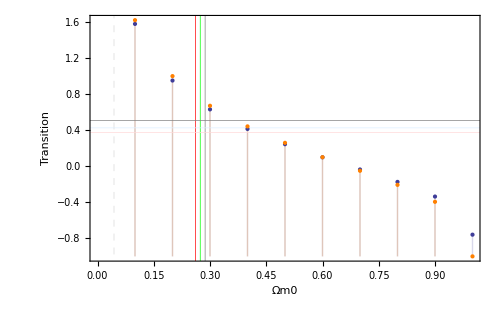

```mathematica
discretepldecΩm0I2CCPL=DiscretePlot[{ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.02,-1.02,0.2],ztr[Ωm0I2CCPL,1-Ωm0I2CCPL]},{Ωm0I2CCPL,0,1,0.1},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.044,Dashed},{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},ImageSize->500,FrameLabel->{"Ωm0","Transition"}]//Quiet
```

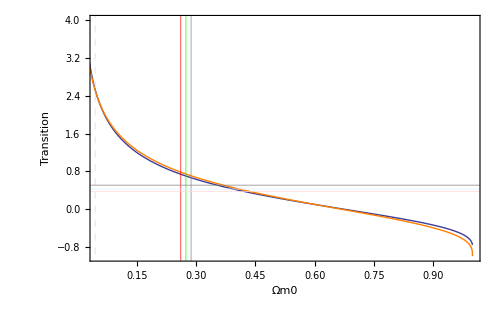

```mathematica
pldecΩm0I2CCPL=Plot[{ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.02,-1.02,0.2],ztr[Ωm0I2CCPL,1-Ωm0I2CCPL]},{Ωm0I2CCPL,0,1},PlotRange->{{0.05,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0.05,-1},Frame->True,GridLines->{{{0.044,Dashed},{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},PlotLegend->{"Q=-0.02 H ρ_d","LCDM"},LegendPosition->{0.0,-0.05},LegendShadow->None,ImageSize->500,FrameLabel->{"Ωm0","Transition"}]//Quiet
```

```mathematica
plztrI2CCPL[ξI2CCPL_,w0I2CCPL_,w1I2CCPL_,color_,{ranges_:0,rangee_:1}]:=Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{ranges,rangee},{-1,4}},PlotStyle->color,AxesOrigin->{0,-1},Frame->True,FrameLabel->{"Ωm0","Transtion"}];
```

```mathematica
(* Do not evaluate this cell if not necessary. *)
plztrI2CCPLManSum=Manipulate[Show[{plztrI2CCPL[ξI2CCPL,w0I2CCPL,w1I2CCPL,Orange,{0,1}],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},Graphics[{Gray,Rectangle[Scaled[{0.261,.2752}],Scaled[{0.287,.3016}]]},Frame->True],GridLines->{{},{{0,Dashed}}},FrameLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_d, CPL: Transition ~ Ωm0"],{{ξI2CCPL,-0.4,"Interaction"},-1,0,Appearance->"Open"},{{w0I2CCPL,-1.02,"CPL EoS w0"},-2,-0.3,Appearance->"Open"},{{w1I2CCPL,0.6,"CPL EoS w1"},-0.2,1,Appearance->"Open"},Delimiter,Style["Orange is for interacting CPL model with Q=ξ H ρ_m",Medium],ControlPlacement->{Right,Right,Right},SaveDefinitions->True]//Quiet
```

```mathematica
plztrExamI2CCPLSum=Grid[{{Show[{plztrI2CCPL[-0.1,-1,0.6,Orange,{0,1}],plztrI2CCPL[-0.3,-1,0.6,{Blue,Dashed},{0,1}],plztrI2CCPL[-0.6,-1,0.6,{Green,Dotted},{0,1}],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},Graphics[{Gray,Rectangle[Scaled[{0.261,.2752}],Scaled[{0.287,.3016}]]},Frame->True],GridLines->{{},{{0,Dashed}}},Epilog->Inset[Framed[Style["Orange: w0=-1,w1=0.6,ξ=-0.1\n Blue dashed:w0=-1,w1=0.6,ξ=-0.3\n Green dotted:w0=-1,w1=0.6,ξ=-0.6\n Pink: LCDM",10],Background->LightGreen,FrameStyle->None],{0.3,3.5},{Left,Top}],FrameLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_d, CPL: Transition ~ Ωm0",ImageSize->400],Show[{plztrI2CCPL[-0.3,-1,0.1,Red,{0,1}],plztrI2CCPL[-0.3,-1,0.4,{Purple,Dotted},{0,1}],plztrI2CCPL[-0.3,-1,0.8,{Magenta,Dashed},{0,1}],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},Graphics[{Gray,Rectangle[Scaled[{0.261,.2752}],Scaled[{0.287,.3016}]]},Frame->True],GridLines->{{},{{0,Dashed}}},Epilog->Inset[Framed[Style["Red: w0=-1,w1=0.1,ξ=-0.3\n Magenta dashed:w0=-1,w1=0.8,ξ=-0.3\n Purple dotted:w0=-1,w1=0.4,ξ=-0.3\n Pink: LCDM",10],Background->LightGreen,FrameStyle->None],{0.3,3.5},{Left,Top}],FrameLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_d, CPL: Transition ~ Ωm0",ImageSize->400]}}]//Quiet
```

-Graphics-

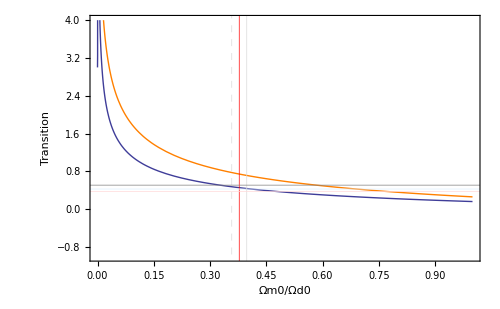

```mathematica
pldecrI2CCPL=Plot[{ztrrI2CCPL[rI2CCPL,-0.6,-1.02,0.6],ztrr[rI2CCPL]},{rI2CCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.358,Dashed},{0.378,Directive[Red]},0.398},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},PlotLegend->{"CPL,Q=-0.6 H ρ_d","LCDM"},LegendPosition->{0.0,-0.05},LegendShadow->None,ImageSize->500,FrameLabel->{"Ωm0/Ωd0","Transition"}]//Quiet
```

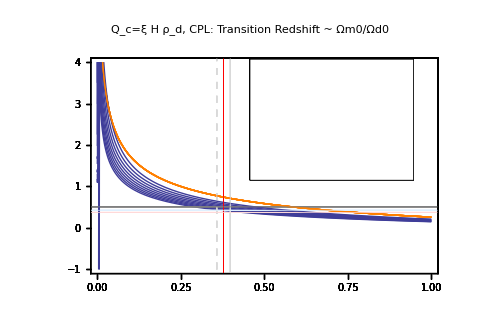

```mathematica
pltransrI2CCPLDense=Show[Table[Plot[{ztrrI2CCPL[rI2CCPL,ξI2CCPL,-1.02,0.6],ztrr[rI2CCPL]},{rI2CCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.358,Dashed},{0.378,Directive[Red]},0.398},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},PlotLegend->{"CPL,Q=ξ H ρ_d,\n with ξ∈(-0.8,0) step=0.1","LCDM"},LegendPosition->{0.0,-0.05},LegendShadow->None],{ξI2CCPL,-0.8,0,0.1}],ImageSize->500,FrameLabel->{"Ωm0/Ωd0","Transition"},PlotLabel->"Q_c=ξ H ρ_d, CPL: Transition Redshift ~ Ωm0/Ωd0",ImageSize->500]//Quiet
```

#### Find out allowed region of coupling constant

To find out the region of ξ, set w=-1 and Ωd0=1-Ωm0. Let the ztr-Ωm0 line cross points (0.287,0.508) and (0.261, 0.376).

```mathematica
Off[FindRoot::nlnum]
Off[ReplaceAll::reps]
ztrI2CCPL[Ωm0I2CCPL,Ωd0I2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]
On[FindRoot::nlnum]
On[ReplaceAll::reps]
```

NIntegrate::inumr: The integrand ⅇ^-3\ w1I2CCPL + 3\ w1I2CCPL/1 + tmp\ (1 + tmp)^-1 + 3\ (w0I2CCPL + w1I2CCPL) + ξI2CCPL has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.}}.

NIntegrate::inumr: The integrand ⅇ^-3.\ w1I2CCPL + 3.\ w1I2CCPL/1.  + tmp\ (1.  + tmp)^-1. + 3.\ (w0I2CCPL + w1I2CCPL) + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0., 3.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

z/.FindRoot[(1+3 (w0I2CCPL+(w1I2CCPL z)/(1+z))) ΩdI2CCPL[Ωd0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]+ΩmI2CCPLtest[Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]==0,{z,3}]

```mathematica
(* ztrICCPL[0.287,1-0.287,ξICCPL1,-1.02,0.6]==0.508 *)
```

```mathematica
ξI2CCPLffunc[Ωm0I2CCPL_,Ωd0I2CCPL_,w0I2CCPL_,w1I2CCPL_,data_]:=ξI2CCPL/.FindRoot[ztrI2CCPL[Ωm0I2CCPL,Ωd0I2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==data,{ξI2CCPL,-0.6}]
```

```mathematica
ξI2CCPLf2[Ωm0I2CCPL_,Ωd0I2CCPL_,w0I2CCPL_,w1I2CCPL_]:=ξI2CCPL/.FindRoot[ztrI2CCPL[Ωm0I2CCPL,Ωd0I2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==0.508,{ξI2CCPL,-0.6}]
```

```mathematica
ξI2CCPLf1[Ωm0I2CCPL_,Ωd0I2CCPL_,w0I2CCPL_,w1I2CCPL_]:=ξI2CCPL/.FindRoot[ztrI2CCPL[Ωm0I2CCPL,Ωd0I2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==0.376,{ξI2CCPL,-0.6}]
```

Cross the Center of best fit. (0.274,0.426)

```mathematica
ξI2CCPLfc[Ωm0I2CCPL_,Ωd0I2CCPL_,w0I2CCPL_,w1I2CCPL_]:=ξI2CCPL/.FindRoot[ztrI2CCPL[Ωm0I2CCPL,Ωd0I2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==0.426,{ξI2CCPL,-0.6}]
```

According to the data of transition redshift.

```mathematica
ξI2CCPLf2[w0I2CCPL_,w1I2CCPL_]:=ξI2CCPLffunc[0.287,1-0.287,w0I2CCPL,w1I2CCPL,0.508]
```

```mathematica
ξI2CCPLf1[w0I2CCPL_,w1I2CCPL_]:=ξI2CCPLffunc[0.261,1-0.261,w0I2CCPL,w1I2CCPL,0.376]
```

```mathematica
ξI2CCPLfc[w0I2CCPL_,w1I2CCPL_]:=ξI2CCPLffunc[0.274,1-0.274,w0I2CCPL,w1I2CCPL,0.426]
```

An example

```mathematica
Off[FindRoot::nlnum]
Off[ReplaceAll::reps]
{ξI2CCPLf1[-1.02,0.6],ξI2CCPLfc[-1.02,0.6],ξI2CCPLf2[-1.02,0.6]}
On[FindRoot::nlnum]
On[ReplaceAll::reps]
```

NIntegrate::inumr: The integrand ⅇ^-1.8 + 1.8/1 + tmp\ (1 + tmp)^-2.26 + ξI2CCPL has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.}}.

NIntegrate::inumr: The integrand ⅇ^-1.8 + 1.8/1.  + tmp\ (1.  + tmp)^-2.26 + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0., 3.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{-1.24538,-0.758365,-0.251702}

```mathematica
ξI2CCPLrffunc[rI2CCPL_,w0I2CCPL_,w1I2CCPL_,data_]:=ξI2CCPL/.FindRoot[ztrrI2CCPL[rI2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==data,{ξI2CCPL,-0.6}]
```

```mathematica
ξI2CCPLrf2[rI2CCPL_,w0I2CCPL_,w1I2CCPL_]:=ξI2CCPL/.FindRoot[ztrrI2CCPL[rI2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==0.508,{ξI2CCPL,-0.6}]
```

```mathematica
ξI2CCPLrf1[rI2CCPL_,w0I2CCPL_,w1I2CCPL_]:=ξI2CCPL/.FindRoot[ztrrI2CCPL[rI2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==0.376,{ξI2CCPL,-0.6}]
```

Cross the Center of best fit. (0.358,0.426)

```mathematica
ξI2CCPLrfc[rI2CCPL_,w0I2CCPL_,w1I2CCPL_]:=ξI2CCPL/.FindRoot[ztrrI2CCPL[rI2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==0.426,{ξI2CCPL,-0.6}]
```

According to the data of transition redshift.

```mathematica
ξI2CCPLrf2[w0I2CCPL_,w1I2CCPL_]:=ξI2CCPLrffunc[0.398,w0I2CCPL,w1I2CCPL,0.508]
```

```mathematica
ξI2CCPLrf1[w0I2CCPL_,w1I2CCPL_]:=ξI2CCPLrffunc[0.358,w0I2CCPL,w1I2CCPL,0.376]
```

```mathematica
ξI2CCPLrfc[w0I2CCPL_,w1I2CCPL_]:=ξI2CCPLrffunc[0.378,w0I2CCPL,w1I2CCPL,0.426]
```

An example

```mathematica
Off[FindRoot::nlnum]
Off[ReplaceAll::reps]
{ξI2CCPLrf1[-1.02,0.6],ξI2CCPLrfc[-1.02,0.6],ξI2CCPLrf2[-1.02,0.6]}
On[FindRoot::nlnum]
On[ReplaceAll::reps]
```

NIntegrate::inumr: The integrand ⅇ^-1.8 + 1.8/1 + tmp\ (1 + tmp)^-2.26 + ξI2CCPL has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.}}.

NIntegrate::inumr: The integrand ⅇ^-1.8 + 1.8/1.  + tmp\ (1.  + tmp)^-2.26 + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0., 3.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{-1.21472,-0.755302,-0.269941}

```mathematica
(* Do not evaluate it unless it is necessary. *)
Off[FindRoot::nlnum]
Off[ReplaceAll::reps]
fitξI2CCPLManSum=Manipulate[Grid[{{numPlot["(",{ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]},")",{-1.5,1}],Plot[w0I2CCPL+w1I2CCPL temp/(temp+1),{temp,-0.9,10}]}}],{{w0I2CCPL,-1.02,"Equation of State w0"},-2,-0.47,Appearance->"Open"},{{w1I2CCPL,0.6,"Equation of State w1"},-1,1,Appearance->"Open"},Delimiter,Style["This is the fitting result from transition redshift data.",Bold],Delimiter,"The parenthesis shows the upper and lower value \n while the verticle line show the center value.",Style["\n The three numbers are left value, center value, right value respectively."],Delimiter,Delimiter,Style["Slide to see how do the two parameters affect the coupling constant results."],ControlPlacement->{Bottom,Bottom},SaveDefinitions->True]
```

```mathematica
(*
On[FindRoot::nlnum]
On[ReplaceAll::reps]
*)
```

#### Quintom Case

The transition redshift. Six groups of parameters.
(-1, 0.1)  (-1, 0.2)  (-0.9,0.1)
(-1, -0.1)  (-1, -0.2)  (-1.1,-0.1)
In two plots, 
(-1, 0.1)  (-1, 0.2)  (-1, -0.1)  (-1, -0.2) 
(-1, 0.1)   (-0.9,0.1)  (-1, -0.1)   (-1.1,-0.1)

```mathematica
pltI2CCPLEoSfunc[w0I2CCPL_,w1I2CCPL_,color_]:=Plot[{w0I2CCPL+w1I2CCPL z/(1+z)},{z,-0.99,10},PlotStyle->color,AxesLabel->{"z","w"}];
```

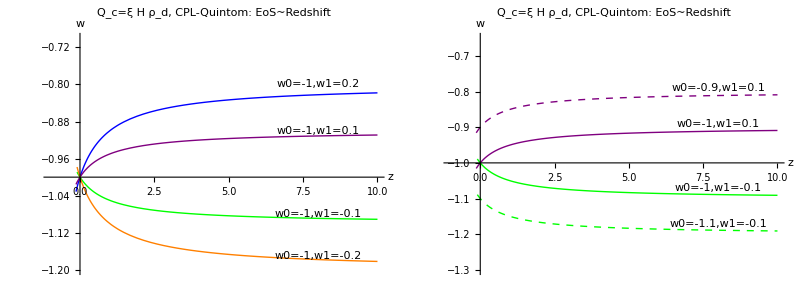

```mathematica
plEoSI2CCPLQuintomSum=Grid[{{Show[pltI2CCPLEoSfunc[-1,0.2,Blue],pltI2CCPLEoSfunc[-1,0.1,Purple],pltI2CCPLEoSfunc[-1,-0.1,Green],pltI2CCPLEoSfunc[-1,-0.2,Orange],PlotRange->{{-0.99,10},{-1.2,-0.7}},AxesOrigin->{0,-1},ImageSize->400,PlotLabel->"Q_c=ξ H ρ_d, CPL-Quintom: EoS~Redshift",Epilog->{Inset[Framed[Style["w0=-1,w1=0.2",10,Blue],Background->None,FrameStyle->None],{8,-0.80},{0,0}],Inset[Framed[Style["w0=-1,w1=0.1",10,Purple],Background->None,FrameStyle->None],{8,-0.9},{0,0}],Inset[Framed[Style["w0=-1,w1=-0.1",10,Green],Background->None,FrameStyle->None],{8,-1.08},{0,0}],Inset[Framed[Style["w0=-1,w1=-0.2",10,Orange],Background->None,FrameStyle->None],{8,-1.17},{0,0}]}],Show[pltI2CCPLEoSfunc[-1,0.1,Purple],pltI2CCPLEoSfunc[-0.9,0.1,{Purple,Dashed}],pltI2CCPLEoSfunc[-1,-0.1,Green],pltI2CCPLEoSfunc[-1.1,-0.1,{Green,Dashed}],PlotRange->{{-1,10},{-1.3,-0.65}},AxesOrigin->{0,-1},ImageSize->400,PlotLabel->"Q_c=ξ H ρ_d, CPL-Quintom: EoS~Redshift",Epilog->{Inset[Framed[Style["w0=-0.9,w1=0.1",10,Purple],Background->None,FrameStyle->None],{8,-0.79},{0,0}],Inset[Framed[Style["w0=-1,w1=0.1",10,Bold,Purple],Background->None,FrameStyle->None],{8,-0.89},{0,0}],Inset[Framed[Style["w0=-1,w1=-0.1",10,Bold,Green],Background->None,FrameStyle->None],{8,-1.07},{0,0}],Inset[Framed[Style["w0=-1.1,w1=-0.1",10,Green],Background->None,FrameStyle->None],{8,-1.17},{0,0}]}]}}]
```

“Purple line:(-1,0.1)─ Blue line: (-1,0.2) Green line:(-1,-0.1)\n─ Pink line:LCDM”
“Purple Dashed:(-0.9,0.1)  Green Dashed:(-1.1,0.1)”

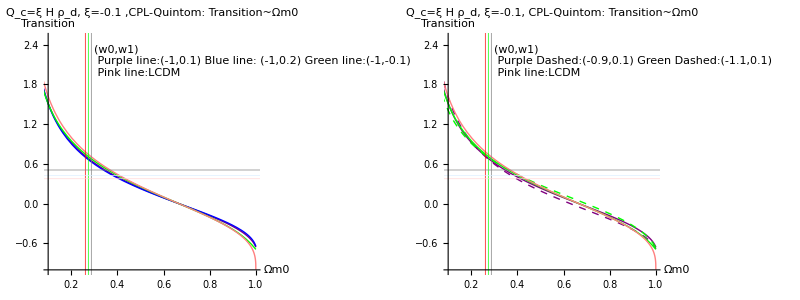

```mathematica
plztrI2CCPLQuintomSum=Grid[{{Show[{plztrI2CCPL[-0.1,-1,0.1,Purple,{0.1,1}],plztrI2CCPL[-0.1,-1,0.2,Blue,{0.1,1}],plztrI2CCPL[-0.1,-1,-0.1,Green,{0.1,1}],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0.1,1},{-1,3}},PlotStyle->Pink,AxesOrigin->{0.1,-1}]},GridLines->{{{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},AxesOrigin->{0.1,-1},PlotRange->{{0.1,1},{-1,2.5}},Frame->False,AxesLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_d, ξ=-0.1 ,CPL-Quintom: Transition~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple line:(-1,0.1) Blue line: (-1,0.2) Green line:(-1,-0.1)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.3,2.4},{Left,Top}],ImageSize->400],Show[{plztrI2CCPL[-0.1,-1,0.1,Purple,{0.1,1}],plztrI2CCPL[-0.1,-0.9,0.1,{Purple,Dashed},{0.1,1}],plztrI2CCPL[-0.1,-1,-0.1,Green,{0.1,1}],plztrI2CCPL[-0.1,-1.1,-0.1,{Green,Dashed},{0.1,1}],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0.1,1},{-1,3}},PlotStyle->Pink,AxesOrigin->{0.1,-1}]},GridLines->{{{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},AxesOrigin->{0.1,-1},PlotRange->{{0.1,1},{-1,2.5}},Frame->False,AxesLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_d, ξ=-0.1, CPL-Quintom: Transition~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple Dashed:(-0.9,0.1) Green Dashed:(-1.1,0.1)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.3,2.4},{Left,Top}],ImageSize->400]}}]//Quiet
```

As for the effect of EoS, we can split it to w0 effect and w1 effect.

First construct the plot function.

```mathematica
(*
pltξvw0I2CCPL[w1I2CCPL_,w0I2CCPLs_,w0I2CCPLe_]:=Plot[{ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]},{w0I2CCPL,w0I2CCPLs,w0I2CCPLe}]
*)
```

Choose the values from Reference 3. w0 = -1.087 ± 0.096,

```mathematica
ξvwExamI2CCPLQuintom={Block[{w0I2CCPL=-1,w1I2CCPL=-0.1},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-1,w1I2CCPL=0},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-1,w1I2CCPL=0.1},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-0.9,w1I2CCPL=0.1},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-1.1,w1I2CCPL=-0.1},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}]}
```

NIntegrate::inumr: The integrand ⅇ^0.3  - 0.3/1 + tmp\ (1 + tmp)^-4.3 + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.}}.

NIntegrate::inumr: The integrand ⅇ^0.3  - 0.3/1.  + tmp\ (1.  + tmp)^-4.3 + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0., 3.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

FindRoot::nlnum: The function value {17.536  - 2.02294\ 4.^-0.3 + ξI2CCPL - 17.536\ ξI2CCPL\ NIntegrate[Exp[0.3  + Times[« 2 »]]\ (1.  + tmp)^-4.3 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.726, -1, -0.1, ξI2CCPL, z] + ΩmI2CCPLtest[0.726, 0.274, -1, -0.1, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {16.704  - 2.05916\ 4.^-0.3 + ξI2CCPL - 16.704\ ξI2CCPL\ NIntegrate[Exp[0.3  + Times[« 2 »]]\ (1.  + tmp)^-4.3 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.739, -1, -0.1, ξI2CCPL, z] + ΩmI2CCPLtest[0.739, 0.261, -1, -0.1, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {18.368  - 1.98672\ 4.^-0.3 + ξI2CCPL - 18.368\ ξI2CCPL\ NIntegrate[Exp[0.3  + Times[« 2 »]]\ (1.  + tmp)^-4.3 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.713, -1, -0.1, ξI2CCPL, z] + ΩmI2CCPLtest[0.713, 0.287, -1, -0.1, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

{{{-1,-0.1},-1.21004,-1.73137,-0.653393},{{-1,0},-1.15265,-1.66715,-0.605615},{{-1,0.1},-1.09155,-1.59939,-0.553918},{{-0.9,0.1},-0.94736,-1.40905,-0.463859},{{-1.1,-0.1},-1.28331,-1.84354,-0.680925}}

```mathematica
tabξvwExamI2CCPLQuintom=Grid[Prepend[Prepend[ξvwExamI2CCPLQuintom,{"{w0,w1}","Center","Lower","Upper"}],{"ξ results for Q_c=ξ H ρ_d, CPL,Quintom.",SpanFromLeft}],Frame->All,Background->{{LightGray,None},{LightGreen,LightGray,None}},Alignment->Center,ItemSize->8]
```

ξ results for Q_c=ξ H ρ_d, CPL,Quintom. |  |  | 
{w0,w1} | Center | Lower | Upper
{-1,-0.1} | -1.21004 | -1.73137 | -0.653393
{-1,0} | -1.15265 | -1.66715 | -0.605615
{-1,0.1} | -1.09155 | -1.59939 | -0.553918
{-0.9,0.1} | -0.94736 | -1.40905 | -0.463859
{-1.1,-0.1} | -1.28331 | -1.84354 | -0.680925

```mathematica
pltfitξI2CCPLfunc[w0I2CCPL_,w1I2CCPL_]:=Grid[{{numPlot["(",{ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]},")",{-2,1}]},{Plot[w0I2CCPL+w1I2CCPL temp/(temp+1),{temp,-0.9,10},Epilog->Inset[Framed[Style[{w0I2CCPL,w1I2CCPL},10],Background->LightYellow],{Center,Center},{Center,Center}]]}}];
```

```mathematica
pltfitξI2CCPLQuintomSum=Grid[{{pltfitξI2CCPLfunc[-1,0.1],pltfitξI2CCPLfunc[-1,0.2],pltfitξI2CCPLfunc[-1,-0.1]},{pltfitξI2CCPLfunc[-0.9,0.1],pltfitξI2CCPLfunc[-1.1,-0.1]}}]
```

NIntegrate::inumr: The integrand ⅇ^-0.3 + 0.3/1 + tmp\ (1 + tmp)^-3.7 + ξI2CCPL has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.}}.

NIntegrate::inumr: The integrand ⅇ^-0.3 + 0.3/1.  + tmp\ (1.  + tmp)^-3.7 + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0., 3.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

FindRoot::nlnum: The function value {16.704  - 1.04743\ 4.^0.3  + ξI2CCPL - 16.704\ ξI2CCPL\ NIntegrate[Exp[-0.3 + Times[« 2 »]]\ (1.  + tmp)^-3.7 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.739, -1, 0.1, ξI2CCPL, z] + ΩmI2CCPLtest[0.739, 0.261, -1, 0.1, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {17.536  - 1.02901\ 4.^0.3  + ξI2CCPL - 17.536\ ξI2CCPL\ NIntegrate[Exp[-0.3 + Times[« 2 »]]\ (1.  + tmp)^-3.7 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.726, -1, 0.1, ξI2CCPL, z] + ΩmI2CCPLtest[0.726, 0.274, -1, 0.1, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {18.368  - 1.01058\ 4.^0.3  + ξI2CCPL - 18.368\ ξI2CCPL\ NIntegrate[Exp[-0.3 + Times[« 2 »]]\ (1.  + tmp)^-3.7 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.713, -1, 0.1, ξI2CCPL, z] + ΩmI2CCPLtest[0.713, 0.287, -1, 0.1, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

numPlot[(,{-1.59939,-1.09155,-0.553918},),{-2,1}]
-Graphics- | numPlot[(,{-1.52784,-1.02648,-0.497957},),{-2,1}]
-Graphics- | numPlot[(,{-1.73137,-1.21004,-0.653393},),{-2,1}]
-Graphics-
numPlot[(,{-1.40905,-0.94736,-0.463859},),{-2,1}]
-Graphics- | numPlot[(,{-1.84354,-1.28331,-0.680925},),{-2,1}]
-Graphics- |

#### Quintessence

Choose some Quintessence parameters.
(-0.9,-0.05) (-0.8,-0.05)(-0.8,-0.1)

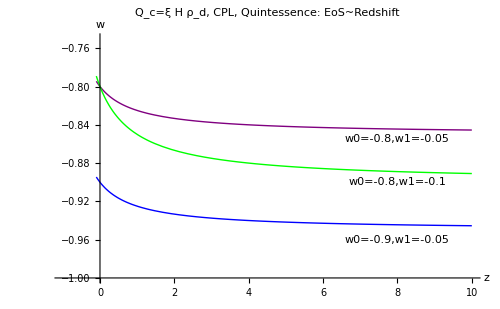

```mathematica
plEoSI2CCPLQuintessenceSum=Grid[{{Show[pltI2CCPLEoSfunc[-0.9,-0.05,Blue],pltI2CCPLEoSfunc[-0.8,-0.05,Purple],pltI2CCPLEoSfunc[-0.8,-0.1,Green],PlotRange->{{-0.99,10},{-1.0,-0.75}},AxesOrigin->{0,-1},Epilog->{Inset[Framed[Style["w0=-0.9,w1=-0.05",10,Blue],Background->None,FrameStyle->None],{8,-0.96},{0,0}],Inset[Framed[Style["w0=-0.8,w1=-0.05",10,Purple],Background->None,FrameStyle->None],{8,-0.855},{0,0}],Inset[Framed[Style["w0=-0.8,w1=-0.1",10,Green],Background->None,FrameStyle->None],{8,-0.9},{0,0}]},PlotLabel->"Q_c=ξ H ρ_d, CPL, Quintessence: EoS~Redshift",ImageSize->500]}}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {-1.0027}. NIntegrate obtained 6.12819×10^93 - 1.20272×10^94\ ⅈ and 1.34985×10^94 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {-1.00216}. NIntegrate obtained 3.93838313043837×10^3757 - 7.72951210650262×10^3757\ ⅈ and 9.16137714372885×10^3757 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {-1.00205}. NIntegrate obtained 7.25839576488893×10^2124 - 1.42454037812851×10^2125\ ⅈ and 1.68843149227054×10^2125 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

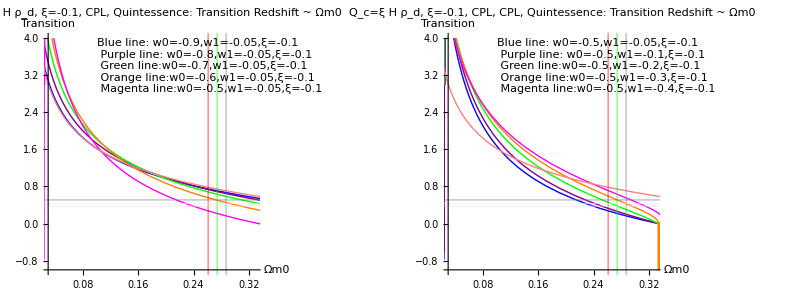

```mathematica
plztrI2CCPLQuintessenceSum=Grid[{{Show[{Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.9,-0.05],{Ωm0I2CCPL,0.01,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Blue,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.8,-0.05],{Ωm0I2CCPL,0.01,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Purple,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.7,-0.05],{Ωm0I2CCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Green,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.6,-0.05],{Ωm0I2CCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Orange,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.5,-0.05],{Ωm0I2CCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Magenta,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0.01,0.94},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},GridLines->{{{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},AxesOrigin->{0.03,-1},PlotRange->{{0.03,0.33},Automatic},Frame->False,AxesLabel->{"Ωm0","Transition"},Epilog->Inset[Framed[Style["Blue line: w0=-0.9,w1=-0.05,ξ=-0.1\n Purple line: w0=-0.8,w1=-0.05,ξ=-0.1\n Green line:w0=-0.7,w1=-0.05,ξ=-0.1\n Orange line:w0=-0.6,w1=-0.05,ξ=-0.1\n Magenta line:w0=-0.5,w1=-0.05,ξ=-0.1",10],Background->LightGreen,FrameStyle->None],{0.1,4},{Left,Top}],PlotLabel->"Q_c=ξ H ρ_d, ξ=-0.1, CPL, Quintessence: Transition Redshift ~ Ωm0",ImageSize->400],Show[{Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.5,-0.05],{Ωm0I2CCPL,0.01,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Blue,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.5,-0.1],{Ωm0I2CCPL,0.01,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Purple,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.5,-0.2],{Ωm0I2CCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Green,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.5,-0.3],{Ωm0I2CCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Orange,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.5,-0.4],{Ωm0I2CCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Magenta,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0.01,0.94},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},GridLines->{{{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},AxesOrigin->{0.03,-1},PlotRange->{{0.03,0.33},Automatic},Frame->False,AxesLabel->{"Ωm0","Transition"},Epilog->Inset[Framed[Style["Blue line: w0=-0.5,w1=-0.05,ξ=-0.1\n Purple line: w0=-0.5,w1=-0.1,ξ=-0.1\n Green line:w0=-0.5,w1=-0.2,ξ=-0.1\n Orange line:w0=-0.5,w1=-0.3,ξ=-0.1\n Magenta line:w0=-0.5,w1=-0.4,ξ=-0.1",10],Background->LightGreen,FrameStyle->None],{0.1,4},{Left,Top}],PlotLabel->"Q_c=ξ H ρ_d, ξ=-0.1, CPL, CPL, Quintessence: Transition Redshift ~ Ωm0",ImageSize->400]}}]
```

As for the effect of EoS, we can split it to w0 effect and w1 effect.

Choose some values of w0 and w1 causually.

```mathematica
ξvwExamI2CCPLQuintessence={Block[{w0I2CCPL=-0.9,w1I2CCPL=-0.05},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-0.8,w1I2CCPL=-0.05},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-0.8,w1I2CCPL=-0.1},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}]}
```

NIntegrate::inumr: The integrand ⅇ^0.15  - 0.15/1 + tmp\ (1 + tmp)^-3.85 + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.}}.

NIntegrate::inumr: The integrand ⅇ^0.15  - 0.15/1.  + tmp\ (1.  + tmp)^-3.85 + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0., 3.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

FindRoot::nlnum: The function value {17.536  - 1.47256\ 4.^0.15  + ξI2CCPL - 17.536\ ξI2CCPL\ NIntegrate[Exp[0.15  + Times[« 2 »]]\ (1.  + tmp)^-3.85 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.726, -0.9, -0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.726, 0.274, -0.9, -0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {16.704  - 1.49893\ 4.^0.15  + ξI2CCPL - 16.704\ ξI2CCPL\ NIntegrate[Exp[0.15  + Times[« 2 »]]\ (1.  + tmp)^-3.85 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.739, -0.9, -0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.739, 0.261, -0.9, -0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {18.368  - 1.44619\ 4.^0.15  + ξI2CCPL - 18.368\ ξI2CCPL\ NIntegrate[Exp[0.15  + Times[« 2 »]]\ (1.  + tmp)^-3.85 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.713, -0.9, -0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.713, 0.287, -0.9, -0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

{{{-0.9,-0.05},-1.05994,-1.53267,-0.561052},{{-0.8,-0.05},-0.881934,-1.30148,-0.445082},{{-0.8,-0.1},-0.926183,-1.35,-0.483467}}

```mathematica
tabξvwExamI2CCPLQuintessence=Grid[Prepend[Prepend[ξvwExamI2CCPLQuintessence,{"{w0,w1}","Center","Lower","Upper"}],{"ξ results for Q_c=ξ H ρ_d, CPL,Quintessence.",SpanFromLeft}],Frame->All,Background->{{LightGray,None},{LightGreen,LightGray,None}},Alignment->Center,ItemSize->8]
```

ξ results for Q_c=ξ H ρ_d, CPL,Quintessence. |  |  | 
{w0,w1} | Center | Lower | Upper
{-0.9,-0.05} | -1.05994 | -1.53267 | -0.561052
{-0.8,-0.05} | -0.881934 | -1.30148 | -0.445082
{-0.8,-0.1} | -0.926183 | -1.35 | -0.483467

```mathematica
pltfitξI2CCPLQuintessenceSum=Grid[{{pltfitξI2CCPLfunc[-0.9,-0.05],pltfitξI2CCPLfunc[-0.8,-0.05],pltfitξI2CCPLfunc[-0.8,-0.1]}}]
```

NIntegrate::inumr: The integrand ⅇ^0.15  - 0.15/1 + tmp\ (1 + tmp)^-3.85 + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.}}.

NIntegrate::inumr: The integrand ⅇ^0.15  - 0.15/1.  + tmp\ (1.  + tmp)^-3.85 + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0., 3.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

FindRoot::nlnum: The function value {16.704  - 1.49893\ 4.^0.15  + ξI2CCPL - 16.704\ ξI2CCPL\ NIntegrate[Exp[0.15  + Times[« 2 »]]\ (1.  + tmp)^-3.85 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.739, -0.9, -0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.739, 0.261, -0.9, -0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {17.536  - 1.47256\ 4.^0.15  + ξI2CCPL - 17.536\ ξI2CCPL\ NIntegrate[Exp[0.15  + Times[« 2 »]]\ (1.  + tmp)^-3.85 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.726, -0.9, -0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.726, 0.274, -0.9, -0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {18.368  - 1.44619\ 4.^0.15  + ξI2CCPL - 18.368\ ξI2CCPL\ NIntegrate[Exp[0.15  + Times[« 2 »]]\ (1.  + tmp)^-3.85 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.713, -0.9, -0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.713, 0.287, -0.9, -0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

numPlot[(,{-1.53267,-1.05994,-0.561052},),{-2,1}]
-Graphics- | numPlot[(,{-1.30148,-0.881934,-0.445082},),{-2,1}]
-Graphics- | numPlot[(,{-1.35,-0.926183,-0.483467},),{-2,1}]
-Graphics-

#### Phantom

Some parameters that give us a phantom mode
(-1.1,0.05) (-1.2,0.05) (-1.2,0.1)

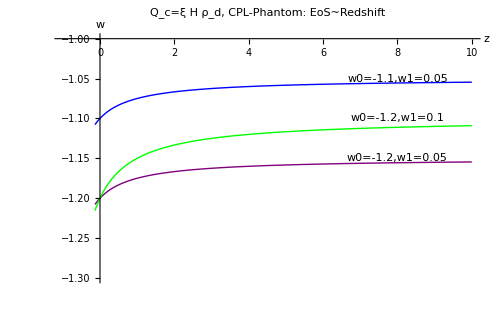

```mathematica
plEoSI2CCPLPhantomSum=Grid[{{Show[pltI2CCPLEoSfunc[-1.1,0.05,Blue],pltI2CCPLEoSfunc[-1.2,0.05,Purple],pltI2CCPLEoSfunc[-1.2,0.1,Green],PlotRange->{{-0.99,10},{-1.3,-1}},AxesOrigin->{0,-1},Epilog->{Inset[Framed[Style["w0=-1.1,w1=0.05",10,Blue],Background->None,FrameStyle->None],{8,-1.05},{0,0}],Inset[Framed[Style["w0=-1.2,w1=0.05",10,Purple],Background->None,FrameStyle->None],{8,-1.15},{0,0}],Inset[Framed[Style["w0=-1.2,w1=0.1",10,Green],Background->None,FrameStyle->None],{8,-1.1},{0,0}]},PlotLabel->"Q_c=ξ H ρ_d, CPL-Phantom: EoS~Redshift",ImageSize->500]}}]
```

```mathematica
plztrI2CCPLPhantomSum=Grid[{{Show[{plztrI2CCPL[-0.1,-1.1,0.05,Blue,{0,1}],plztrI2CCPL[-0.1,-1.2,0.05,Purple,{0,1}],plztrI2CCPL[-0.1,-1.2,0.1,Green,{0,1}],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},Graphics[{Gray,Rectangle[Scaled[{0.261,.2752}],Scaled[{0.287,.3016}]]},Frame->True],AxesOrigin->{0,-1},Frame->False,AxesLabel->{"Ωm0","Transition"},Epilog->Inset[Framed[Style["Blue line: w0=-1.1,w1=0.05,ξ=-0.1\n Purple line: w0=-1.2,w1=0.05,ξ=-0.1\n Green line:w0=-1.2,w1=0.1,ξ=-0.1",10],Background->LightGreen,FrameStyle->None],{0.35,3.5},{0,0}],PlotLabel->"Q_c=ξ H ρ_d, CPL-Phantom: Transition ~ Ωm0",ImageSize->500]}}]
```

-Graphics-

As for the effect of EoS, we can split it to w0 effect and w1 effect.

Choose some values of w0 and w1 causually.

```mathematica
ξvwExamI2CCPLPhantom={Block[{w0I2CCPL=-1.1,w1I2CCPL=0.05},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-1.2,w1I2CCPL=0.05},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-1.2,w1I2CCPL=0.1},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}]}
```

NIntegrate::inumr: The integrand ⅇ^-0.15 + 0.15/1 + tmp\ (1 + tmp)^-4.15 + ξI2CCPL has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.}}.

NIntegrate::inumr: The integrand ⅇ^-0.15 + 0.15/1.  + tmp\ (1.  + tmp)^-4.15 + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0., 3.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

FindRoot::nlnum: The function value {17.536  - 1.41914\ 4.^-0.15 + ξI2CCPL - 17.536\ ξI2CCPL\ NIntegrate[Exp[-0.15 + Times[« 2 »]]\ (1.  + tmp)^-4.15 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.726, -1.1, 0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.726, 0.274, -1.1, 0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {16.704  - 1.44456\ 4.^-0.15 + ξI2CCPL - 16.704\ ξI2CCPL\ NIntegrate[Exp[-0.15 + Times[« 2 »]]\ (1.  + tmp)^-4.15 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.739, -1.1, 0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.739, 0.261, -1.1, 0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {18.368  - 1.39373\ 4.^-0.15 + ξI2CCPL - 18.368\ ξI2CCPL\ NIntegrate[Exp[-0.15 + Times[« 2 »]]\ (1.  + tmp)^-4.15 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.713, -1.1, 0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.713, 0.287, -1.1, 0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

{{{-1.1,0.05},-1.21257,-1.76337,-0.623591},{{-1.2,0.05},-1.266,-1.8517,-0.635863},{{-1.2,0.1},-1.24569,-1.82849,-0.619702}}

```mathematica
tabξvwExamI2CCPLPhantom=Grid[Prepend[Prepend[ξvwExamI2CCPLPhantom,{"{w0,w1}","Center","Lower","Upper"}],{"ξ results for Q_c=ξ H ρ_d, CPL,Phantom.",SpanFromLeft}],Frame->All,Background->{{LightGray,None},{LightGreen,LightGray,None}},Alignment->Center,ItemSize->8]
```

ξ results for Q_c=ξ H ρ_d, CPL,Phantom. |  |  | 
{w0,w1} | Center | Lower | Upper
{-1.1,0.05} | -1.21257 | -1.76337 | -0.623591
{-1.2,0.05} | -1.266 | -1.8517 | -0.635863
{-1.2,0.1} | -1.24569 | -1.82849 | -0.619702

```mathematica
pltfitξI2CCPLPhantomSum=Grid[{{pltfitξI2CCPLfunc[-1.1,0.05],pltfitξI2CCPLfunc[-1.2,0.05],pltfitξI2CCPLfunc[-1.2,0.1]}}]
```

NIntegrate::inumr: The integrand ⅇ^-0.15 + 0.15/1 + tmp\ (1 + tmp)^-4.15 + ξI2CCPL has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.}}.

NIntegrate::inumr: The integrand ⅇ^-0.15 + 0.15/1.  + tmp\ (1.  + tmp)^-4.15 + ξI2CCPL
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0., 3.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

FindRoot::nlnum: The function value {16.704  - 1.44456\ 4.^-0.15 + ξI2CCPL - 16.704\ ξI2CCPL\ NIntegrate[Exp[-0.15 + Times[« 2 »]]\ (1.  + tmp)^-4.15 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.739, -1.1, 0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.739, 0.261, -1.1, 0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {17.536  - 1.41914\ 4.^-0.15 + ξI2CCPL - 17.536\ ξI2CCPL\ NIntegrate[Exp[-0.15 + Times[« 2 »]]\ (1.  + tmp)^-4.15 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.726, -1.1, 0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.726, 0.274, -1.1, 0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {18.368  - 1.39373\ 4.^-0.15 + ξI2CCPL - 18.368\ ξI2CCPL\ NIntegrate[Exp[-0.15 + Times[« 2 »]]\ (1.  + tmp)^-4.15 + ξI2CCPL, {tmp, 0., 3.}]}
 is not a list of numbers with dimensions {1} at {z} = {3.}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdI2CCPL[0.713, -1.1, 0.05, ξI2CCPL, z] + ΩmI2CCPLtest[0.713, 0.287, -1.1, 0.05, ξI2CCPL, z] == 0, {z, 3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

numPlot[(,{-1.76337,-1.21257,-0.623591},),{-2,1}]
-Graphics- | numPlot[(,{-1.8517,-1.266,-0.635863},),{-2,1}]
-Graphics- | numPlot[(,{-1.82849,-1.24569,-0.619702},),{-2,1}]
-Graphics-